# Speed Comparison as Vertices is increased.

### Code

Below is the code need to run run the plots that are located below this section of code.

Here is a function that generates a random graph with the number of edges between  and  :

```mathematica
graphgen[n_]:= Module[{g},
While@Not@ConnectedGraphQ[ g=RandomGraph[{n ,RandomInteger[{n-1, n(n-1)/2}] },VertexLabels-> Placed[Automatic,Center],VertexSize->0.15]];
Return[g]
]
```

Function to generate a graph with the minim  amount of edges:

```mathematica
graphgenlow[n_]:= Module[{g},
While@Not@ConnectedGraphQ[ g=RandomGraph[{n ,n-1},VertexLabels-> Placed[Automatic,Center],VertexSize->0.15]];
Return[g]
]
```

Function to create the polynomial system regarding the graph and the number of colours k:

```mathematica
kgraphploy[g_, k_]:= Module[{vert,absvert,edge,absedge, vertpoly, vars,edgepoly, graphpoly}, 
vert=VertexList[g];
absvert=Length[vert];


edge=List @@@EdgeList[g];
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]];

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpoly=Join[vertpoly,edgepoly];

Return[graphpoly];
]
```

Here is the block of code that runs through increasing number vertices and records the time for the three different orderings for the Buchberger method. The code also records the number of variables and also the number of expressions seen in both the original polynomial system and the reduce Groebner basis. Lastly the code will plot the data. For large  upperlimit of vertices and the colours Mathematica may take awhile to compute and in some cases crash. Hence only small values of these can be choose.

Number of Vertices: 3

Number of Vertices: 4

Number of Vertices: 5

Number of Vertices: 6

Number of Vertices: 7

Number of Vertices: 8

Number of Vertices: 9

Number of Vertices: 10

Number of Vertices: 11

Number of Vertices: 12

Number of Vertices: 13

Number of Vertices: 14

Number of Vertices: 15

Number of Vertices: 16

Number of Vertices: 17

Number of Vertices: 18

Number of Vertices: 19

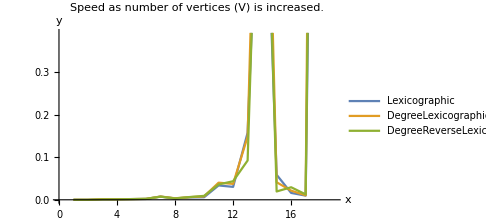
-Graphics-Number Vetrices (Starting at 3)Times (Seconds)

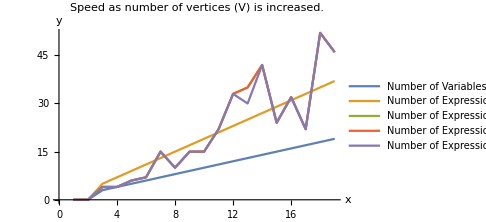
-Graphics-Number Vetrices (Starting at 3)Number

```mathematica
upperlimit = 19;
colours = 3;
glist = Table[ kgraphploy[graphgenlow[i] ,colours] , {i,3,upperlimit}];
timebuiltina1 = {0,0};
timebuiltina2 = {0,0};
timebuiltina3 = {0,0};
numterms ={0,0};
numtermsRGL ={0,0};
numtermsRGDL ={0,0};
numtermsRGDRL ={0,0};
numvar = {0,0};
listbases ={};
For[i=0, i <= Length[glist]-1,  i++ ; { 
Print["Number of Vertices: ", i+2],
{time1, basesa1} = AbsoluteTiming[GroebnerBasis[glist[[i]],Variables[glist[[i]]], Method->"Buchberger", MonomialOrder-> Lexicographic ]];
{time2, basesa2} = AbsoluteTiming[GroebnerBasis[glist[[i]],Variables[glist[[i]]], Method->"Buchberger", MonomialOrder-> DegreeLexicographic ]];
{time3, basesa3} = AbsoluteTiming[GroebnerBasis[glist[[i]],Variables[glist[[i]]], Method->"Buchberger", MonomialOrder-> DegreeReverseLexicographic ]];
AppendTo[listbases, basesa1],
AppendTo[timebuiltina1, time1],
AppendTo[timebuiltina2, time2],
AppendTo[timebuiltina3, time3],
AppendTo[numvar, Length[Variables[ basesa1 ]] ],
AppendTo[numterms, Length[ glist[[i]] ]],
AppendTo[numtermsRGL, Length[basesa1]],
AppendTo[numtermsRGDL, Length[basesa2]],
AppendTo[numtermsRGDRL, Length[basesa3]],
} ]
plot1 = Labeled[ListLinePlot[{timebuiltina1,timebuiltina2,timebuiltina3}, PlotLegends->{"Lexicographic","DegreeLexicographic", "DegreeReverseLexicographic"},PlotLabel->"Speed as number of vertices (V) is increased.", AxesOrigin->{0,0}, AxesLabel->{"x","y"},ImageSize->Medium ],{"Number Vetrices (Starting at 3)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
plot2 = Labeled[ListLinePlot[{numvar, numterms,numtermsRGL,numtermsRGDL,numtermsRGDRL}, PlotLegends->{"Number of Variables", "Number of Expressions", "Number of Expressions Lex", "Number of Expressions Deg Lex", "Number of Expressions Deg Rev Lex" },PlotLabel->"Speed as number of vertices (V) is increased.",AxesOrigin->{0, 0}, AxesLabel->{"x","y"},ImageSize->Medium ],{"Number Vetrices (Starting at 3)","Number"},{Bottom,Left},RotateLabel->True]
```

Function to generate a graph with the about the middle  amount of edges :

```mathematica
graphgenmid[n_]:= Module[{g},
While@Not@ConnectedGraphQ[ g=RandomGraph[{n ,Floor[ First[Midpoint[{ {n-1,0},{ (n(n-1))/2,0}}]]]},VertexLabels-> Placed[Automatic,Center],VertexSize->0.15]];
Return[g]
]
```

The code below is to compute and plot, but is system resources heavy and may cause crashes.

```mathematica
upperlimit = 19;
colours = 4;
glist1 = Table[ kgraphploy[graphgenlow[i] ,colours] , {i,3,upperlimit}];
timebuiltina11 = {0,0};
timebuiltina21 = {0,0};
timebuiltina31 = {0,0};
numterms1 ={0,0};
numtermsRGL1 ={0,0};
numtermsRGDL1 ={0,0};
numtermsRGDRL1 ={0,0};
numvar1 = {0,0};
listbases1 ={};
For[i=0, i <= Length[glist1]-1,  i++ ; { 
Print["Number of Vertices: ", i+2],
{time1, basesa11} = AbsoluteTiming[GroebnerBasis[glist1[[i]],Variables[glist1[[i]]], Method->"Buchberger", MonomialOrder-> Lexicographic ]];
{time2, basesa21} = AbsoluteTiming[GroebnerBasis[glist1[[i]],Variables[glist1[[i]]], Method->"Buchberger", MonomialOrder-> DegreeLexicographic ]];
{time3, basesa31} = AbsoluteTiming[GroebnerBasis[glist1[[i]],Variables[glist1[[i]]], Method->"Buchberger", MonomialOrder-> DegreeReverseLexicographic ]];
AppendTo[listbases1, basesa1],
AppendTo[timebuiltina11, time1],
AppendTo[timebuiltina21, time2],
AppendTo[timebuiltina31, time3],
AppendTo[numvar, Length[Variables[ basesa1 ]] ],
AppendTo[numterms, Length[ glist[[i]] ]],
AppendTo[numtermsRGL, Length[basesa1]],
AppendTo[numtermsRGDL, Length[basesa2]],
AppendTo[numtermsRGDRL, Length[basesa3]],
} ]
plot1 = Labeled[ListLinePlot[{timebuiltina1,timebuiltina2,timebuiltina3}, PlotLegends->{"Lexicographic","DegreeLexicographic", "DegreeReverseLexicographic"},PlotLabel->"Speed as number of vertices (V) is increased.", AxesOrigin->{0,0}, AxesLabel->{"x","y"},ImageSize->Medium ],{"Number Vetrices (Starting at 3)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
plot2 = Labeled[ListLinePlot[{numvar, numterms,numtermsRGL,numtermsRGDL,numtermsRGDRL}, PlotLegends->{"Number of Variables", "Number of Expressions", "Number of Expressions Lex", "Number of Expressions Deg Lex", "Number of Expressions Deg Rev Lex" },PlotLabel->"Speed as number of vertices (V) is increased.",AxesOrigin->{0, 0}, AxesLabel->{"x","y"},ImageSize->Medium ],{"Number Vetrices (Starting at 3)","Number"},{Bottom,Left},RotateLabel->True]
```